```mathematica
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace2\\NumberTheory"];
<<NumberTheory`
```

```mathematica
(* NumberTheory Package Test *)
Table[{n,n^2,n^3},{n,1,5}]//tf
Select[nCollatz[27],OddQ]
nFaulhaber[2,5]
```

1 | 1 | 1
2 | 4 | 8
3 | 9 | 27
4 | 16 | 64
5 | 25 | 125

{27,41,31,47,71,107,161,121,91,137,103,155,233,175,263,395,593,445,167,251,377,283,425,319,479,719,1079,1619,2429,911,1367,2051,3077,577,433,325,61,23,35,53,5,1}

55

## Queue MMa.SE Questions

https://math.stackexchange.com/questions/136417/what-is-so-interesting-about-the-zeroes-of-the-riemann-zeta-function/136488#136488

### Q.1

```mathematica
DirichletConvolve[1,u[n],n,m]//FullForm
```

DivisorSum[m,Function[u[Slot[1]]]]

### Q.2

```mathematica
DirichletTransform[Abs[MoebiusMu[n]],n,s]
```

Zeta[s]/Zeta[2 s]

```mathematica
DirichletTransform[MoebiusMu[n]^2,n,s]
```

DirichletTransform[MoebiusMu[n]^2,n,s]

```mathematica
Table[{k,Abs[MoebiusMu[k]],MoebiusMu[k]^2},{k,1,6}]//tf
```

1 | 1 | 1
2 | 1 | 1
3 | 1 | 1
4 | 0 | 0
5 | 1 | 1
6 | 1 | 1

## Topic

### Definition / Theorem

This is text.

#### Example

# Algebraic Number Theory

Introduction

A crash course in Ring Theory

## Basic Definitions

### TBD: Def. Ring

[ TBD ]

#### Example

### TBD: Def. Subring

[ TBD ]

#### Example

### TBD: Def. Unit

[ TBD ]

#### Example

### TBD: Def. Field

[ TBD ]

#### Example

## Ideals, Homomorphisms, and Quotients

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Principal Ideals

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Operations on Ideals

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Prime and Maximal Ideals

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

Lattices

## Group Structure of Lattices

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Linear Algebra over ℤ

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Computing with Ideals

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Lattice Quotients

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

Arithmetic in Q[d]

## Quadratic Fields

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## The Ring of Integers

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Unique Factorization of Ideals: The Roadmap

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Noether Rings

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Standard Form of an Ideal

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## The Ideal Norm

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Fractional Ideals

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Unique Factorization of Ideals

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Prime Ideals in O

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

The Ideal Class Group and the Geometry of Numbers

Continued Fractions

Quadratic Forms

Notes

## tmp-1

```mathematica
Needs["AbstractAlgebra`Master`"]
```

```mathematica
SwitchStructureTo[Ring];
```

```mathematica
R1=Z[5,I,Structure->Ring]
CayleyTables[R1,Mode->Visual]
```

Ringoid[{0,ⅈ,2 ⅈ,3 ⅈ,4 ⅈ,1,1+ⅈ,1+2 ⅈ,1+3 ⅈ,1+4 ⅈ,2,2+ⅈ,2+2 ⅈ,2+3 ⅈ,2+4 ⅈ,3,3+ⅈ,3+2 ⅈ,3+3 ⅈ,3+4 ⅈ,4,4+ⅈ,4+2 ⅈ,4+3 ⅈ,4+4 ⅈ},-Addition-,-Multiplication-]

+ | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16 | g17 | g18 | g19 | g20 | g21 | g22 | g23 | g24 | g25
g1 | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16 | g17 | g18 | g19 | g20 | g21 | g22 | g23 | g24 | g25
g2 | g2 | g3 | g4 | g5 | g1 | g7 | g8 | g9 | g10 | g6 | g12 | g13 | g14 | g15 | g11 | g17 | g18 | g19 | g20 | g16 | g22 | g23 | g24 | g25 | g21
g3 | g3 | g4 | g5 | g1 | g2 | g8 | g9 | g10 | g6 | g7 | g13 | g14 | g15 | g11 | g12 | g18 | g19 | g20 | g16 | g17 | g23 | g24 | g25 | g21 | g22
g4 | g4 | g5 | g1 | g2 | g3 | g9 | g10 | g6 | g7 | g8 | g14 | g15 | g11 | g12 | g13 | g19 | g20 | g16 | g17 | g18 | g24 | g25 | g21 | g22 | g23
g5 | g5 | g1 | g2 | g3 | g4 | g10 | g6 | g7 | g8 | g9 | g15 | g11 | g12 | g13 | g14 | g20 | g16 | g17 | g18 | g19 | g25 | g21 | g22 | g23 | g24
g6 | g6 | g7 | g8 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16 | g17 | g18 | g19 | g20 | g21 | g22 | g23 | g24 | g25 | g1 | g2 | g3 | g4 | g5
g7 | g7 | g8 | g9 | g10 | g6 | g12 | g13 | g14 | g15 | g11 | g17 | g18 | g19 | g20 | g16 | g22 | g23 | g24 | g25 | g21 | g2 | g3 | g4 | g5 | g1
g8 | g8 | g9 | g10 | g6 | g7 | g13 | g14 | g15 | g11 | g12 | g18 | g19 | g20 | g16 | g17 | g23 | g24 | g25 | g21 | g22 | g3 | g4 | g5 | g1 | g2
g9 | g9 | g10 | g6 | g7 | g8 | g14 | g15 | g11 | g12 | g13 | g19 | g20 | g16 | g17 | g18 | g24 | g25 | g21 | g22 | g23 | g4 | g5 | g1 | g2 | g3
g10 | g10 | g6 | g7 | g8 | g9 | g15 | g11 | g12 | g13 | g14 | g20 | g16 | g17 | g18 | g19 | g25 | g21 | g22 | g23 | g24 | g5 | g1 | g2 | g3 | g4
g11 | g11 | g12 | g13 | g14 | g15 | g16 | g17 | g18 | g19 | g20 | g21 | g22 | g23 | g24 | g25 | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8 | g9 | g10
g12 | g12 | g13 | g14 | g15 | g11 | g17 | g18 | g19 | g20 | g16 | g22 | g23 | g24 | g25 | g21 | g2 | g3 | g4 | g5 | g1 | g7 | g8 | g9 | g10 | g6
g13 | g13 | g14 | g15 | g11 | g12 | g18 | g19 | g20 | g16 | g17 | g23 | g24 | g25 | g21 | g22 | g3 | g4 | g5 | g1 | g2 | g8 | g9 | g10 | g6 | g7
g14 | g14 | g15 | g11 | g12 | g13 | g19 | g20 | g16 | g17 | g18 | g24 | g25 | g21 | g22 | g23 | g4 | g5 | g1 | g2 | g3 | g9 | g10 | g6 | g7 | g8
g15 | g15 | g11 | g12 | g13 | g14 | g20 | g16 | g17 | g18 | g19 | g25 | g21 | g22 | g23 | g24 | g5 | g1 | g2 | g3 | g4 | g10 | g6 | g7 | g8 | g9
g16 | g16 | g17 | g18 | g19 | g20 | g21 | g22 | g23 | g24 | g25 | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8 | g9 | g10 | g11 | g12 | g13 | g14 | g15
g17 | g17 | g18 | g19 | g20 | g16 | g22 | g23 | g24 | g25 | g21 | g2 | g3 | g4 | g5 | g1 | g7 | g8 | g9 | g10 | g6 | g12 | g13 | g14 | g15 | g11
g18 | g18 | g19 | g20 | g16 | g17 | g23 | g24 | g25 | g21 | g22 | g3 | g4 | g5 | g1 | g2 | g8 | g9 | g10 | g6 | g7 | g13 | g14 | g15 | g11 | g12
g19 | g19 | g20 | g16 | g17 | g18 | g24 | g25 | g21 | g22 | g23 | g4 | g5 | g1 | g2 | g3 | g9 | g10 | g6 | g7 | g8 | g14 | g15 | g11 | g12 | g13
g20 | g20 | g16 | g17 | g18 | g19 | g25 | g21 | g22 | g23 | g24 | g5 | g1 | g2 | g3 | g4 | g10 | g6 | g7 | g8 | g9 | g15 | g11 | g12 | g13 | g14
g21 | g21 | g22 | g23 | g24 | g25 | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16 | g17 | g18 | g19 | g20
g22 | g22 | g23 | g24 | g25 | g21 | g2 | g3 | g4 | g5 | g1 | g7 | g8 | g9 | g10 | g6 | g12 | g13 | g14 | g15 | g11 | g17 | g18 | g19 | g20 | g16
g23 | g23 | g24 | g25 | g21 | g22 | g3 | g4 | g5 | g1 | g2 | g8 | g9 | g10 | g6 | g7 | g13 | g14 | g15 | g11 | g12 | g18 | g19 | g20 | g16 | g17
g24 | g24 | g25 | g21 | g22 | g23 | g4 | g5 | g1 | g2 | g3 | g9 | g10 | g6 | g7 | g8 | g14 | g15 | g11 | g12 | g13 | g19 | g20 | g16 | g17 | g18
g25 | g25 | g21 | g22 | g23 | g24 | g5 | g1 | g2 | g3 | g4 | g10 | g6 | g7 | g8 | g9 | g15 | g11 | g12 | g13 | g14 | g20 | g16 | g17 | g18 | g19  Add.KEY for Add(Z[5, I]): label used → element: {g1→0,g2→ⅈ,g3→2 ⅈ,g4→3 ⅈ,g5→4 ⅈ,g6→1,g7→1+ⅈ,g8→1+2 ⅈ,g9→1+3 ⅈ,g10→1+4 ⅈ,g11→2,g12→2+ⅈ,g13→2+2 ⅈ,g14→2+3 ⅈ,g15→2+4 ⅈ,g16→3,g17→3+ⅈ,g18→3+2 ⅈ,g19→3+3 ⅈ,g20→3+4 ⅈ,g21→4,g22→4+ⅈ,g23→4+2 ⅈ,g24→4+3 ⅈ,g25→4+4 ⅈ}* | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16 | g17 | g18 | g19 | g20 | g21 | g22 | g23 | g24 | g25
g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1
g2 | g1 | g21 | g16 | g11 | g6 | g2 | g22 | g17 | g12 | g7 | g3 | g23 | g18 | g13 | g8 | g4 | g24 | g19 | g14 | g9 | g5 | g25 | g20 | g15 | g10
g3 | g1 | g16 | g6 | g21 | g11 | g3 | g18 | g8 | g23 | g13 | g5 | g20 | g10 | g25 | g15 | g2 | g17 | g7 | g22 | g12 | g4 | g19 | g9 | g24 | g14
g4 | g1 | g11 | g21 | g6 | g16 | g4 | g14 | g24 | g9 | g19 | g2 | g12 | g22 | g7 | g17 | g5 | g15 | g25 | g10 | g20 | g3 | g13 | g23 | g8 | g18
g5 | g1 | g6 | g11 | g16 | g21 | g5 | g10 | g15 | g20 | g25 | g4 | g9 | g14 | g19 | g24 | g3 | g8 | g13 | g18 | g23 | g2 | g7 | g12 | g17 | g22
g6 | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16 | g17 | g18 | g19 | g20 | g21 | g22 | g23 | g24 | g25
g7 | g1 | g22 | g18 | g14 | g10 | g7 | g3 | g24 | g20 | g11 | g13 | g9 | g5 | g21 | g17 | g19 | g15 | g6 | g2 | g23 | g25 | g16 | g12 | g8 | g4
g8 | g1 | g17 | g8 | g24 | g15 | g8 | g24 | g15 | g1 | g17 | g15 | g1 | g17 | g8 | g24 | g17 | g8 | g24 | g15 | g1 | g24 | g15 | g1 | g17 | g8
g9 | g1 | g12 | g23 | g9 | g20 | g9 | g20 | g1 | g12 | g23 | g12 | g23 | g9 | g20 | g1 | g20 | g1 | g12 | g23 | g9 | g23 | g9 | g20 | g1 | g12
g10 | g1 | g7 | g13 | g19 | g25 | g10 | g11 | g17 | g23 | g4 | g14 | g20 | g21 | g2 | g8 | g18 | g24 | g5 | g6 | g12 | g22 | g3 | g9 | g15 | g16
g11 | g1 | g3 | g5 | g2 | g4 | g11 | g13 | g15 | g12 | g14 | g21 | g23 | g25 | g22 | g24 | g6 | g8 | g10 | g7 | g9 | g16 | g18 | g20 | g17 | g19
g12 | g1 | g23 | g20 | g12 | g9 | g12 | g9 | g1 | g23 | g20 | g23 | g20 | g12 | g9 | g1 | g9 | g1 | g23 | g20 | g12 | g20 | g12 | g9 | g1 | g23
g13 | g1 | g18 | g10 | g22 | g14 | g13 | g5 | g17 | g9 | g21 | g25 | g12 | g4 | g16 | g8 | g7 | g24 | g11 | g3 | g20 | g19 | g6 | g23 | g15 | g2
g14 | g1 | g13 | g25 | g7 | g19 | g14 | g21 | g8 | g20 | g2 | g22 | g9 | g16 | g3 | g15 | g10 | g17 | g4 | g11 | g23 | g18 | g5 | g12 | g24 | g6
g15 | g1 | g8 | g15 | g17 | g24 | g15 | g17 | g24 | g1 | g8 | g24 | g1 | g8 | g15 | g17 | g8 | g15 | g17 | g24 | g1 | g17 | g24 | g1 | g8 | g15
g16 | g1 | g4 | g2 | g5 | g3 | g16 | g19 | g17 | g20 | g18 | g6 | g9 | g7 | g10 | g8 | g21 | g24 | g22 | g25 | g23 | g11 | g14 | g12 | g15 | g13
g17 | g1 | g24 | g17 | g15 | g8 | g17 | g15 | g8 | g1 | g24 | g8 | g1 | g24 | g17 | g15 | g24 | g17 | g15 | g8 | g1 | g15 | g8 | g1 | g24 | g17
g18 | g1 | g19 | g7 | g25 | g13 | g18 | g6 | g24 | g12 | g5 | g10 | g23 | g11 | g4 | g17 | g22 | g15 | g3 | g16 | g9 | g14 | g2 | g20 | g8 | g21
g19 | g1 | g14 | g22 | g10 | g18 | g19 | g2 | g15 | g23 | g6 | g7 | g20 | g3 | g11 | g24 | g25 | g8 | g16 | g4 | g12 | g13 | g21 | g9 | g17 | g5
g20 | g1 | g9 | g12 | g20 | g23 | g20 | g23 | g1 | g9 | g12 | g9 | g12 | g20 | g23 | g1 | g23 | g1 | g9 | g12 | g20 | g12 | g20 | g23 | g1 | g9
g21 | g1 | g5 | g4 | g3 | g2 | g21 | g25 | g24 | g23 | g22 | g16 | g20 | g19 | g18 | g17 | g11 | g15 | g14 | g13 | g12 | g6 | g10 | g9 | g8 | g7
g22 | g1 | g25 | g19 | g13 | g7 | g22 | g16 | g15 | g9 | g3 | g18 | g12 | g6 | g5 | g24 | g14 | g8 | g2 | g21 | g20 | g10 | g4 | g23 | g17 | g11
g23 | g1 | g20 | g9 | g23 | g12 | g23 | g12 | g1 | g20 | g9 | g20 | g9 | g23 | g12 | g1 | g12 | g1 | g20 | g9 | g23 | g9 | g23 | g12 | g1 | g20
g24 | g1 | g15 | g24 | g8 | g17 | g24 | g8 | g17 | g1 | g15 | g17 | g1 | g15 | g24 | g8 | g15 | g24 | g8 | g17 | g1 | g8 | g17 | g1 | g15 | g24
g25 | g1 | g10 | g14 | g18 | g22 | g25 | g4 | g8 | g12 | g16 | g19 | g23 | g2 | g6 | g15 | g13 | g17 | g21 | g5 | g9 | g7 | g11 | g20 | g24 | g3  Mult.

```mathematica
R2=Z[20,5]
CayleyTables[R2,Mode->Visual]
```

Ringoid[{0,5,10,15},Mod[#1+#2,20]&,Mod[#1 #2,20]&]

+ | 0 | 5 | 10 | 15
0 | 0 | 5 | 10 | 15
5 | 5 | 10 | 15 | 0
10 | 10 | 15 | 0 | 5
15 | 15 | 0 | 5 | 10  Add.* | 0 | 5 | 10 | 15
0 | 0 | 0 | 0 | 0
5 | 0 | 5 | 10 | 15
10 | 0 | 10 | 0 | 10
15 | 0 | 15 | 10 | 5  Mult.

```mathematica
RingQ[R2]
FieldQ[R2]
Units[R2]
```

True

False

{5,15}

```mathematica
FieldQ[Z[30,6]]
```

True

```mathematica
M=Mat[Z[2],{2,2}]
```

-Mat_2(Z[2])-

```mathematica
Map[#//mf&,Domain[M]]
```

{(0 | 0
0 | 0),(0 | 0
0 | 1),(0 | 0
1 | 0),(0 | 0
1 | 1),(0 | 1
0 | 0),(0 | 1
0 | 1),(0 | 1
1 | 0),(0 | 1
1 | 1),(1 | 0
0 | 0),(1 | 0
0 | 1),(1 | 0
1 | 0),(1 | 0
1 | 1),(1 | 1
0 | 0),(1 | 1
0 | 1),(1 | 1
1 | 0),(1 | 1
1 | 1)}

```mathematica
R3=ToRingoid[Mat[Z[2],2]]
```

Ringoid[{{{0,0},{0,0}},{{0,0},{0,1}},{{0,0},{1,0}},{{0,0},{1,1}},{{0,1},{0,0}},{{0,1},{0,1}},{{0,1},{1,0}},{{0,1},{1,1}},{{1,0},{0,0}},{{1,0},{0,1}},{{1,0},{1,0}},{{1,0},{1,1}},{{1,1},{0,0}},{{1,1},{0,1}},{{1,1},{1,0}},{{1,1},{1,1}}},-Addition-,-Multiplication-]

```mathematica
RingQ[R3]
```

True

```mathematica
CayleyTables[R3,Mode->Visual]
```

+ | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16
g1 | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16
g2 | g2 | g1 | g4 | g3 | g6 | g5 | g8 | g7 | g10 | g9 | g12 | g11 | g14 | g13 | g16 | g15
g3 | g3 | g4 | g1 | g2 | g7 | g8 | g5 | g6 | g11 | g12 | g9 | g10 | g15 | g16 | g13 | g14
g4 | g4 | g3 | g2 | g1 | g8 | g7 | g6 | g5 | g12 | g11 | g10 | g9 | g16 | g15 | g14 | g13
g5 | g5 | g6 | g7 | g8 | g1 | g2 | g3 | g4 | g13 | g14 | g15 | g16 | g9 | g10 | g11 | g12
g6 | g6 | g5 | g8 | g7 | g2 | g1 | g4 | g3 | g14 | g13 | g16 | g15 | g10 | g9 | g12 | g11
g7 | g7 | g8 | g5 | g6 | g3 | g4 | g1 | g2 | g15 | g16 | g13 | g14 | g11 | g12 | g9 | g10
g8 | g8 | g7 | g6 | g5 | g4 | g3 | g2 | g1 | g16 | g15 | g14 | g13 | g12 | g11 | g10 | g9
g9 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16 | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8
g10 | g10 | g9 | g12 | g11 | g14 | g13 | g16 | g15 | g2 | g1 | g4 | g3 | g6 | g5 | g8 | g7
g11 | g11 | g12 | g9 | g10 | g15 | g16 | g13 | g14 | g3 | g4 | g1 | g2 | g7 | g8 | g5 | g6
g12 | g12 | g11 | g10 | g9 | g16 | g15 | g14 | g13 | g4 | g3 | g2 | g1 | g8 | g7 | g6 | g5
g13 | g13 | g14 | g15 | g16 | g9 | g10 | g11 | g12 | g5 | g6 | g7 | g8 | g1 | g2 | g3 | g4
g14 | g14 | g13 | g16 | g15 | g10 | g9 | g12 | g11 | g6 | g5 | g8 | g7 | g2 | g1 | g4 | g3
g15 | g15 | g16 | g13 | g14 | g11 | g12 | g9 | g10 | g7 | g8 | g5 | g6 | g3 | g4 | g1 | g2
g16 | g16 | g15 | g14 | g13 | g12 | g11 | g10 | g9 | g8 | g7 | g6 | g5 | g4 | g3 | g2 | g1  Add.KEY for Add(-Mat   (Z[2])-)
        (2): label used → element: …* | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16
g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1
g2 | g1 | g2 | g3 | g4 | g1 | g2 | g3 | g4 | g1 | g2 | g3 | g4 | g1 | g2 | g3 | g4
g3 | g1 | g1 | g1 | g1 | g2 | g2 | g2 | g2 | g3 | g3 | g3 | g3 | g4 | g4 | g4 | g4
g4 | g1 | g2 | g3 | g4 | g2 | g1 | g4 | g3 | g3 | g4 | g1 | g2 | g4 | g3 | g2 | g1
g5 | g1 | g5 | g9 | g13 | g1 | g5 | g9 | g13 | g1 | g5 | g9 | g13 | g1 | g5 | g9 | g13
g6 | g1 | g6 | g11 | g16 | g1 | g6 | g11 | g16 | g1 | g6 | g11 | g16 | g1 | g6 | g11 | g16
g7 | g1 | g5 | g9 | g13 | g2 | g6 | g10 | g14 | g3 | g7 | g11 | g15 | g4 | g8 | g12 | g16
g8 | g1 | g6 | g11 | g16 | g2 | g5 | g12 | g15 | g3 | g8 | g9 | g14 | g4 | g7 | g10 | g13
g9 | g1 | g1 | g1 | g1 | g5 | g5 | g5 | g5 | g9 | g9 | g9 | g9 | g13 | g13 | g13 | g13
g10 | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16
g11 | g1 | g1 | g1 | g1 | g6 | g6 | g6 | g6 | g11 | g11 | g11 | g11 | g16 | g16 | g16 | g16
g12 | g1 | g2 | g3 | g4 | g6 | g5 | g8 | g7 | g11 | g12 | g9 | g10 | g16 | g15 | g14 | g13
g13 | g1 | g5 | g9 | g13 | g5 | g1 | g13 | g9 | g9 | g13 | g1 | g5 | g13 | g9 | g5 | g1
g14 | g1 | g6 | g11 | g16 | g5 | g2 | g15 | g12 | g9 | g14 | g3 | g8 | g13 | g10 | g7 | g4
g15 | g1 | g5 | g9 | g13 | g6 | g2 | g14 | g10 | g11 | g15 | g3 | g7 | g16 | g12 | g8 | g4
g16 | g1 | g6 | g11 | g16 | g6 | g1 | g16 | g11 | g11 | g16 | g1 | g6 | g16 | g11 | g6 | g1  Mult.

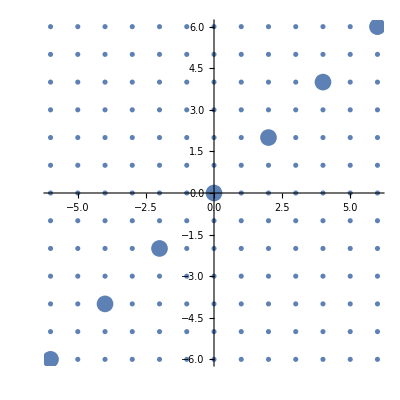

```mathematica
gr=IntegerLatticeGrid[{-6,6},{-6,6},AspectRatio->Automatic];
z=2+2I;
someMultipliers=Table[k,{k,-3,3}];
idealList = someMultipliers * z;
plotOfIdeals=ListPlot[Map[ComplexToPoint,idealList],PlotStyle->{PointSize[0.030],RGBColor[l,0,O]},DisplayFunction->Identity];
Show[{gr,plotOfIdeals}]
```

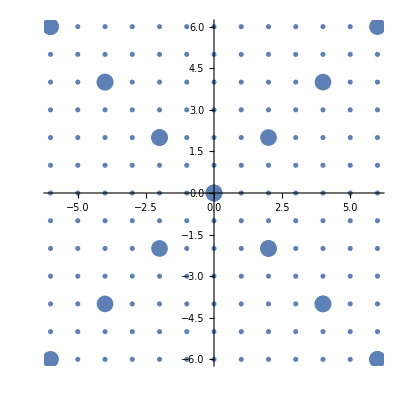

```mathematica
addToIdealList=Table[k I,{k,-3,3}] z;
idealList=Join[idealList,addToIdealList];
plotOfIdeals=ListPlot[Map[ComplexToPoint,idealList],PlotStyle->{PointSize[0.030],RGBColor[l,0,O]},AspectRatio->Automatic,DisplayFunction->Identity];
Show[{gr,plotOfIdeals}]
```

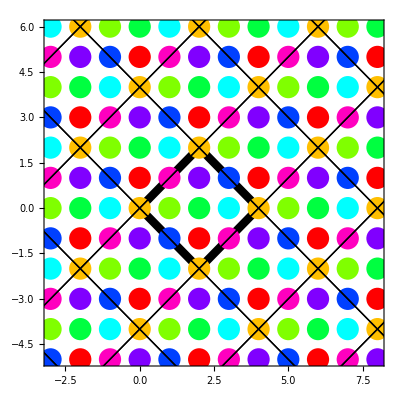

```mathematica
QuotientRing[Z[I],2+2I,Mode->Visual,Form->Representatives]
```

```mathematica
QuotientRing[Z[I],2+2I]
```

Ringoid[{J,1+J,2+J,3+J,(3+ⅈ)+J,(2+ⅈ)+J,(1+ⅈ)+J,(2-ⅈ)+J},-Addition-,-Multiplication-]

```mathematica
R=Z[45];
B1={0,15,30};
B2={0,9,18,27,36};
IdealQ[B1,R]
IdealQ[B2,R]
CayleyTables[QuotientRing[R,B2],Mode->Visual]
```

True

True

+ | NS | 1+NS | 2+NS | 3+NS | 4+NS | 5+NS | 6+NS | 7+NS | 8+NS
NS | NS | 1+NS | 2+NS | 3+NS | 4+NS | 5+NS | 6+NS | 7+NS | 8+NS
1+NS | 1+NS | 2+NS | 3+NS | 4+NS | 5+NS | 6+NS | 7+NS | 8+NS | NS
2+NS | 2+NS | 3+NS | 4+NS | 5+NS | 6+NS | 7+NS | 8+NS | NS | 1+NS
3+NS | 3+NS | 4+NS | 5+NS | 6+NS | 7+NS | 8+NS | NS | 1+NS | 2+NS
4+NS | 4+NS | 5+NS | 6+NS | 7+NS | 8+NS | NS | 1+NS | 2+NS | 3+NS
5+NS | 5+NS | 6+NS | 7+NS | 8+NS | NS | 1+NS | 2+NS | 3+NS | 4+NS
6+NS | 6+NS | 7+NS | 8+NS | NS | 1+NS | 2+NS | 3+NS | 4+NS | 5+NS
7+NS | 7+NS | 8+NS | NS | 1+NS | 2+NS | 3+NS | 4+NS | 5+NS | 6+NS
8+NS | 8+NS | NS | 1+NS | 2+NS | 3+NS | 4+NS | 5+NS | 6+NS | 7+NS  Add.* | NS | 1+NS | 2+NS | 3+NS | 4+NS | 5+NS | 6+NS | 7+NS | 8+NS
NS | NS | NS | NS | NS | NS | NS | NS | NS | NS
1+NS | NS | 1+NS | 2+NS | 3+NS | 4+NS | 5+NS | 6+NS | 7+NS | 8+NS
2+NS | NS | 2+NS | 4+NS | 6+NS | 8+NS | 1+NS | 3+NS | 5+NS | 7+NS
3+NS | NS | 3+NS | 6+NS | NS | 3+NS | 6+NS | NS | 3+NS | 6+NS
4+NS | NS | 4+NS | 8+NS | 3+NS | 7+NS | 2+NS | 6+NS | 1+NS | 5+NS
5+NS | NS | 5+NS | 1+NS | 6+NS | 2+NS | 7+NS | 3+NS | 8+NS | 4+NS
6+NS | NS | 6+NS | 3+NS | NS | 6+NS | 3+NS | NS | 6+NS | 3+NS
7+NS | NS | 7+NS | 5+NS | 3+NS | 1+NS | 8+NS | 6+NS | 4+NS | 2+NS
8+NS | NS | 8+NS | 7+NS | 6+NS | 5+NS | 4+NS | 3+NS | 2+NS | 1+NS  Mult.

## AddTwo via WSTP

```mathematica
SetDirectory["C:/Users/Nilo/__DATA/Mega/DATA/MyTexifyProjects/FreitagBusamExercises/src/Mathematica/WSTP"]
```

C:\Users\Nilo\__DATA\Mega\DATA\MyTexifyProjects\FreitagBusamExercises\src\Mathematica\WSTP

```mathematica
link = Install["./addtwo"]
```

LinkObject[…]

```mathematica
?AddTwo
```

```mathematica
AddTwo[1,3]
```

4

```mathematica
Uninstall[link]
```

./addtwo

## Overzetten naar NotesMMa

```mathematica
{1,21,3,4,1,2}/. 1:>10
```

{10,21,3,4,10,2}

```mathematica
$CloudCreditsAvailable
```

105000

```mathematica
FullForm[(3/2+1/2I)/(1/2)]
(3/2+1/2I)/(1/2)
Complex[1,1]
?Complex
```

Complex[3,1]

3+ⅈ

1+ⅈ

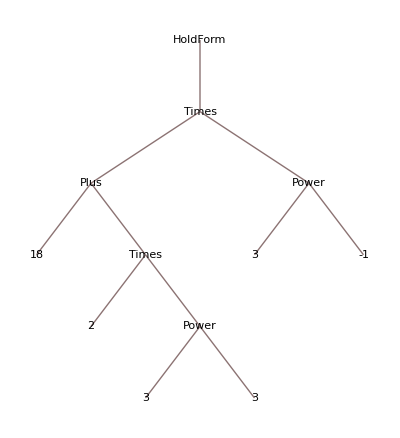

```mathematica
TreeForm[HoldForm[(18+2 3^3)/3]]
```

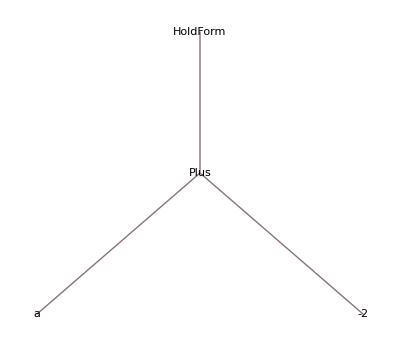

```mathematica
HoldForm[a-2] //TreeForm
```

```mathematica
x:=2
Clear[f]
f[x_,y_]:=x+y
f[3,√2]
f[2,3]
```

3+√2

5

```mathematica
x:=2
Clear[f]
f[x_,y_]=x+y
f[3,√2]
f[2,3]
```

2+y

2+√2

5

```mathematica
Array[Prime,25]/. (x_:> {x,NumberFieldClassNumber[Sqrt[x]]})//Transpose//tf
```

2 | 1
3 | 1
5 | 1
7 | 1
11 | 1
13 | 1
17 | 1
19 | 1
23 | 1
29 | 1
31 | 1
37 | 1
41 | 1
43 | 1
47 | 1
53 | 1
59 | 1
61 | 1
67 | 1
71 | 1
73 | 1
79 | 3
83 | 1
89 | 1
97 | 1